```mathematica
Show[
Table[ParametricPlot[{t+(1-t)Cos[2π s],(1-t) Sin[2π s]},{s,0,1},Axes->None],{t,0,1,.2}],
Table[ParametricPlot[{t+(1-t)Cos[2π s],(1-t) Sin[2π s]},{s,0,1},Axes->None],{t,0.8,1,.05}],
Table[ParametricPlot[{t+(1-t)Cos[2π s],(1-t) Sin[2π s]},{s,0,1},Axes->None],{t,0.95,1,.01}],
Graphics[Line[{{-1.2,0},{1.2,0}}]],
Graphics[Line[{{0,-1.2},{0,1.2}}]]

]
```

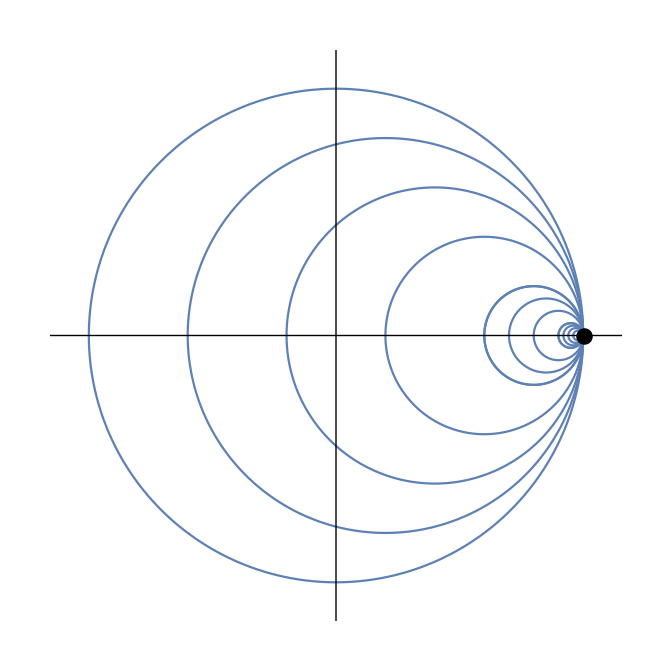

```mathematica
Show[
Plot[(x-3)^2-0.1,{x,-1,5},PlotRange->{{-1,5},{-0.3,1}},Axes->None],
Graphics[Line[{{-1,0},{1,0}}]],
Graphics[Line[{{2,0},{4,0}}]],
Plot[x^2,{x,-1,1}]
]
```

```mathematica
Show[
Graphics[{Opacity[0],EdgeForm[Thick],Rectangle[]}],
Graphics[{Opacity[0],Rectangle[{-.2,-.2}]}],
Graphics[{Opacity[0],Rectangle[]}],
Graphics[Line[{{0.7,0},{0.7,1}}]],
Graphics[Line[{{0,0.8},{1,0.8}}]],
Graphics[{PointSize[Large],Point[{0.7,0.8}]}],
Graphics[{PointSize[Large],Point[{0.7,0}]}],
Graphics[{PointSize[Large],Point[{0,0.8}]}]
]
```